```mathematica
depth = 4;
```

```mathematica
width = 5;
```

```mathematica
PadLeft[IntegerDigits[13, 5], 5]
```

{0,0,0,2,3}

```mathematica
space[init_] := Map[
	(CellularAutomaton[#1, init, 5]&), Range[2^8-1]]
```

```mathematica
ourspace = Join[space[{0,0,0,0,0}], space[{0, 0, 1, 0, 0}]]
```

{{{0,0,0,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,1,1,1,1}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,1,1,1,1}},505,{{0,0,1,0,0},{0,1,1,1,0},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}},{{0,0,1,0,0},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}}}
 |  |  |  |

```mathematica
addRow[r1_, r2_] := MapThread[ (BitXor[#1, #2]&), {r1, r2}]
```

```mathematica
addVectors[v1_, v2_] := MapThread[ (addRow[#1, #2]&), {v1, v2}];
```

```mathematica
{ {0,0, b_,0,0}, rest__} -> {{0,0, BitXor[b],0,0}, rest}
```

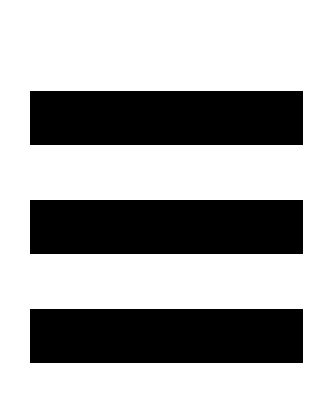

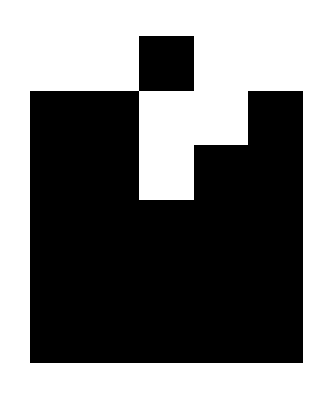

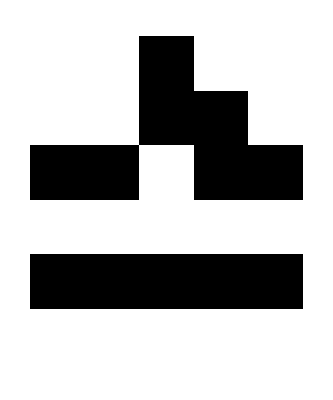

```mathematica
vecA = ourspace[[5]];
vecB = ourspace[[-21]];
ArrayPlot[vecA]
ArrayPlot[vecB]
vecC = addVectors[vecA, vecB];
ArrayPlot[vecC]
MemberQ[ourspace, vecC]
```

```mathematica
MatchQ[ourspace,{{0,0,0,0,0},{0,0,1,1,0},{1,1,0,1,1},{0,0,0,0,0},{1,1,1,1,1},{0,0,0,0,0}}]
```

False

we know 
rule 5 of blank init    +   rule 2^8-21    with single init     =    unknown rule of   single init

```mathematica
addRowCarry[r1_, r2_] := Take[PadLeft[IntegerDigits[FromDigits[r1,2] + FromDigits[r2, 2],2],width],-width]
```

```mathematica
addRowCarry[{0, 0, 1, 1, 0}, {1, 1, 0, 0, 1}]
```

{1,1,1,1,1}

```mathematica
Take[{0,1,1,1,1},-4]
```

{1,1,1,1}

```mathematica
FromDigits[{1, 2, 3},2]
```

11

```mathematica
addVectorsCarry[v1_, v2_] := MapThread[ (addRowCarry[#1, #2]&), {v1, v2}];
```

-Graphics-

-Graphics-

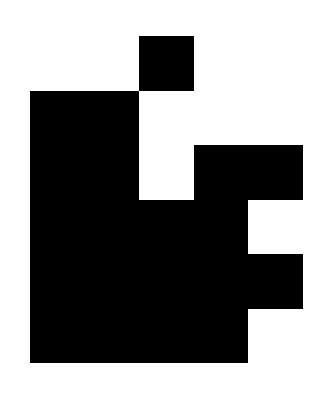

False

```mathematica
vecA = ourspace[[5]];
vecB = ourspace[[-21]];
ArrayPlot[vecA]
ArrayPlot[vecB]
vecC = addVectorsCarry[vecA, vecB];
ArrayPlot[vecC]
MemberQ[ourspace, vecC]
```

```mathematica
{
```

```mathematica
{

{{0,0,0,0,0},
{0,0,0


}
```